## TB NNN

```mathematica
Quit
```

```mathematica
(*Lattice constant*)
a=1.44;    (*look for papers that show this value*)
t=2.75;                            (*t=2.7–2.9 (eV;2.7 is common)*)
Δ=6;
t2A =-0.1 ;(*look for papers that show this value*)
t2B =-0.05;(*https://pubs.aip.org/aip/acp/article-abstract/2005/1/030003/618783/Tight-binding-model-study-of-boron-nitrogen-doped?redirectedFrom=PDF*)
(*Δ=0 for graphene and Δ=5.8 for hBN. t=2.9 graphene and t=2.7. a=2.46 for graphene*)
(*Δ=0 for graphene and Δ=5.8 for hBN. t=2.9 graphene and t=2.7. a=2.46 for graphene*)
(*Real-space lattice vectors*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};
(*Compute area of unit cell*)
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};
delta1=(a1+a2)/3;
delta2=(-2*a1/3+a2/3);
delta3=(a1/3-2*a2/3);
delta4=a1;
delta5=a2;
delta6=-a1;
delta7 = -a2;
delta8=(a2-a1);
delta9=-(a2-a1);
gamma[kx_,ky_]:=Exp[I*(kx*delta1[[1]]+ky*delta1[[2]])]+Exp[I*(kx*delta2[[1]]+ky*delta2[[2]])]+Exp[I*(kx*delta3[[1]]+ky*delta3[[2]])]
gk[kx_,ky_]:=2 (Cos[kx a1[[1]]+ky a1[[2]]]+Cos[kx a2[[1]]+ky a2[[2]]]+Cos[kx (a2-a1)[[1]]+ky (a2-a1)[[2]]]);
H[kx_,ky_]:={{Δ/2+t2A*gk[kx,ky],t*gamma[kx,ky]},{t*Conjugate[gamma[kx,ky]],-Δ/2+t2B*gk[kx,ky]}};
eigenvals[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]]
```

```mathematica
eigenvals[0,-1.7031]
```

{-3.3029,2.85328}

## PLOT Band Structure

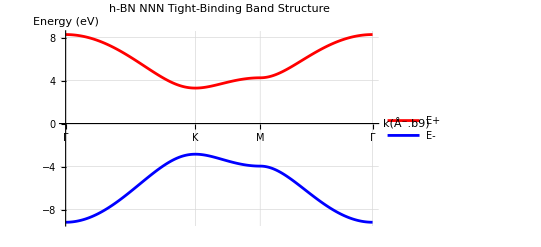

```mathematica
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};

kΓ={0,0};
kK=(1/3)*(b1-b2);
kM=(1/2)*b1;
kPath=Join[Table[(1-s) kΓ+s kK,{s,0,1,0.01}],Table[(1-s) kK+s kM,{s,0,1,0.01}],Table[(1-s) kM+s kΓ,{s,0,1,0.01}]];
kDistances=
Prepend[
Accumulate[
Norm/@Differences[kPath]
],
0
];
bands=eigenvals@@@kPath;
bandsPlus=bands[[All,2]];
bandsMinus=bands[[All,1]];
symmetryPoints={1,Length[kPath]/3,2*Length[kPath]/3,Length[kPath]};
tickPositions=kDistances[[Round[symmetryPoints]]];
tickLabels={"Γ","K","M","Γ"};
ticks=Transpose[{tickPositions,tickLabels}];
bandsPlusData=Transpose[{kDistances,bandsPlus}];
bandsMinusData=Transpose[{kDistances,bandsMinus}];
Show[ListLinePlot[bandsPlusData,Joined->True,PlotStyle->Red,PlotLegends->{"E+"}],ListLinePlot[bandsMinusData,Joined->True,PlotStyle->Blue,PlotLegends->{"E-"}],Ticks->{{{kDistances[[1]],"Γ"},{kDistances[[Length[kPath]/3]],"K"},{kDistances[[2*Length[kPath]/3]],"M"},{kDistances[[Length[kPath]]],"Γ"}},Automatic},AxesLabel->{"k(Å⁻.b9)","Energy (eV)"},GridLines->Automatic,PlotLabel->"h-BN NNN Tight-Binding Band Structure",PlotRange->All]
```

```mathematica
(*bands for a given pair {t2A,t2B}*)
bandsFor[{a2_,b2_}]:=Block[{t2A=a2,t2B=b2,bands},
bands=eigenvals@@@kPath;
{Transpose[{kDistances,bands[[All,2]]}],
(*upper band E+*)Transpose[{kDistances,bands[[All,1]]}]   (*lower band E-*)}];

{bp1,bm1}=bandsFor[{-0.05,-0.1}];
{bp2,bm2}=bandsFor[{0.05,0.1}];
```

```mathematica
ListLinePlot[{bp1,bm1,bp2,bm2},Joined->True,PlotStyle->{Directive[Purple],Directive[Purple],(*bp1,bm1*)Directive[Orange],Directive[Orange]     (*bp2,bm2*)},PlotLegends->{LineLegend[{Directive[Purple],Directive[Orange]},{"( = -0.05,  = -0.10)","( = 0.05,   = 0.10)"}]},Ticks->{ticks,Automatic},AxesLabel->{"k(Å⁻.b9)","Energy (eV)"},GridLines->Automatic,PlotRange->All,PlotLabel->"h-BN TB Band Structure",ImageSize->Large,LabelStyle->Directive[16]]
```

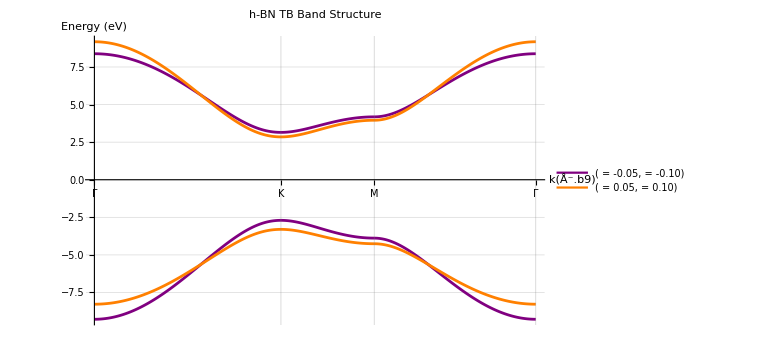

-Graphics-

## Heat map

```mathematica
a=1.44;                                 (*bond length in angstrom*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};

(*nearest neighbors (A->B),each has length a*)
delta1=(a1+a2)/3;
delta2=(-2 a1+a2)/3;
delta3=(a1-2 a2)/3;

(*---2) Reciprocal lattice---*)
area=Det[{a1,a2}];                      (* =(3 Sqrt[3]/2) a^2*)
b1=(2 Pi/area) {a2[[2]],-a2[[1]]};
b2=(2 Pi/area) {-a1[[2]],a1[[1]]};

(*---3) Structure factors---*)
gamma[kx_,ky_]:=Module[{k={kx,ky}},Exp[I k.delta1]+Exp[I k.delta2]+Exp[I k.delta3]];
gk[kx_,ky_]:=Module[{k={kx,ky}},2 (Cos[k.a1]+Cos[k.a2]+Cos[k.(a2-a1)])];

(*---4) High-symmetry points and BZ hexagon---*)
(*six corners generated from three representatives and their negatives*)
K1=(2 b1+b2)/3;          (*three inequivalent corners*)
K2=(b1+2 b2)/3;
K3=(b1-b2)/3;

Ks={K1,-K2,-K3};        (*label these as K*)
Kps={K2,-K1,K3};         (*label these as K'*)

Γpt={0.,0.};

(*order the six corners counterclockwise to draw the hexagon outline*)
allCorners={K1,K2,K3,-K1,-K2,-K3};
orderAngle[p_]:=ArcTan[p[[1]],p[[2]]];
hex=SortBy[allCorners,orderAngle]//N;
hex=Append[hex,First@hex];           (*close the loop*)

(*---5) Tight plot box around the hexagon with a small padding---*)
xmin=Min[hex[[All,1]]];xmax=Max[hex[[All,1]]];
ymin=Min[hex[[All,2]]];ymax=Max[hex[[All,2]]];
pad=0.10 Max[xmax-xmin,ymax-ymin];
xrng={xmin-pad,xmax+pad};
yrng={ymin-pad,ymax+pad};

(*---6) Uniform sampling grid in that rectangle---*)
nx=201;ny=201;
xs=Subdivide[xrng[[1]],xrng[[2]],nx-1];
ys=Subdivide[yrng[[1]],yrng[[2]],ny-1];
```

```mathematica
offVec[pt_,Γ_:{0.,0.},r_:0.07]:=If[Norm[pt-Γ]<10^-12,{r,r},r Normalize[pt-Γ]];
```

```mathematica
t2sumMax=0.15;
zmin=-9 Abs[t2sumMax];
zmax=9 Abs[t2sumMax];
cf=(ColorData["BlueGreenYellow"][Rescale[#,{zmin,zmax}]]&);
```

```mathematica
plotT2pair[a_,b_]:=(t2A=a;t2B=b;t2sum=a+b;
Adata=Flatten[Table[{x,y,t2sum*gk[x,y]},{x,xs},{y,ys}],1];
ListDensityPlot[Adata,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->{xrng,yrng,{zmin,zmax}},PlotLegends->BarLegend[{cf,{zmin,zmax}}],PlotLabel->Row[{"(t2A,t2B)=(",a,", ",b,")"}]]);

plotT2pair[0.05,0.1]
```

-Graphics-

```mathematica
Export["/Users/kimreyesg/Library/CloudStorage/OneDrive-StateUniversityofNewYorkatNewPaltz/2025-II/Undergrad-Research/Michael-Kendra/Asymmetry.png",%613,"PNG"]
```

/Users/kimreyesg/Library/CloudStorage/OneDrive-StateUniversityofNewYorkatNewPaltz/2025-II/Undergrad-Research/Michael-Kendra/Asymmetry.png